Define the marchenko-pastur distribution:

```mathematica
a[α_]:=(1+√α)^2;
b[α_]:=(1-√α)^2;
k[λ_,α_]:=1/(2π λ α)√((a[α]-λ)(λ-b[α]));
Manipulate[Plot[k[λ,α],{λ,0,5},Filling->Bottom,AxesLabel->{λ,"ρ(λ)"}],{α,0.1,2},LabelStyle->Directive[Bold, Medium]]
```

Solve for non-identity covariance:

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

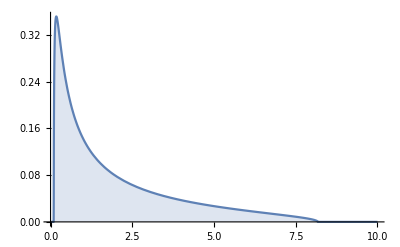

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

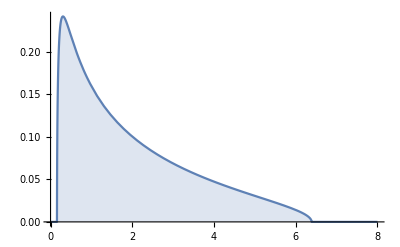

```mathematica
Clear[λ,σ,α,q,f,g]
w[λ_,q_]:=(α(q-1))/(2 σ^2)(-1+√((1-λ+q*λ+3 σ^2)/(1-λ+q*λ-σ^2)));
f[q_]:=α(q-1)(1-(λ(q-1))/(2 σ^2)(-1+√((1-λ(1-q)+3 σ^2)/(1-λ(1-q)-σ^2))));
s=Solve[q==f[q],q];
g[λ_]:=q/.s[[2]];
h[λ_] :=q/.s[[4]];
α=2;
σ=0.92;
u[λ_,σ_]:= 1/(π*α)(Im[w[λ,g[λ]]]+Im[w[λ,h[λ]]])

Plot[u[λ,σ],{λ,0,10},Filling->Axis, PlotRange->All]
```

Save the data to text file

```mathematica
t = Table[{λ,u[λ,σ]},{λ,0.01,10,0.01}];
SetDirectory[NotebookDirectory[]];
Export["model_alpha2_sigma08.txt",t,"Table"];
```

Load data, fit the model:

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
σ | 0.0135438 | 56.6337 | 0.000239147 | 0.999809

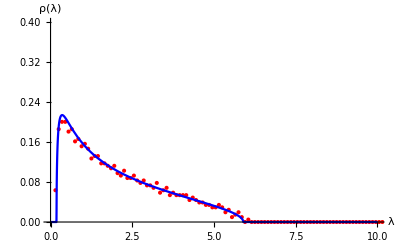

```mathematica
data = Rest[Import["C:\\Users\\owner\\Documents\\Projects\\rnaseq_correlations\\model fit\\pc_data\\sample_15a_filtered_scrambled.csv"]];
α=2.04;
Clear[σ]
fit = NonlinearModelFit[data,{Evaluate[u[λ,σ]],σ>0 && σ<1},{{σ,0.5}},λ];
fit["ParameterTable"] (*Display the best-fit parameters*)
Show[ListPlot[data,PlotStyle->Red, PlotRange->{{0,10},{0,0.4}}, AxesLabel->{λ,"ρ(λ)"},LabelStyle->Directive[Bold, Medium]],Plot[fit[lambda],{lambda,0,10},PlotStyle->Blue, PlotRange->Full]]
```

Save fit data to file:

```mathematica
t=Table[{fit[λ],λ},{λ,0.01,10,0.01}];
SetDirectory[NotebookDirectory[]];
Export["fit_sample_2b.txt",t,"Table"];
```

Maximum likelihood estimator

```mathematica
α=1.99;
R = 10^-4;
data = Import["C:\\Users\\owner\\Documents\\Projects\\rnaseq_correlations\\model fit\\MLE\\pcs_sample_15a.txt","Table"]//Flatten;
M = Table[u[λ,σ],{σ,0.01,0.99,0.01},{λ,data}]
Export["C:\\Users\\owner\\Documents\\Projects\\rnaseq_correlations\\model fit\\MLE\\MLE_matrix_sample_15a.csv",M, "Table"]
```

{1}
 |  |  |  |

C:\Users\owner\Documents\Projects\rnaseq_correlations\model fit\MLE\MLE_matrix_sample_15a.csv

```mathematica
Export["MLE_matrix.csv",M, "Table"]
```

MLE_matrix.csv

```mathematica
ExpandFileName["MLE_matrix.csv"]
```

C:\Users\owner\OneDrive\Documents\MLE_matrix.csv